# Open Quantum Institute - Quantum Hackathon LATAM

## QUBO Mapping & Nested QAOA Implementation

```mathematica
<<Wolfram`QuantumFramework`
```

## Functions

```mathematica
multiQAOAStep[Dmatrix_,ω_,{λ3_,λ4_,σ_,c_}]:=Module[{
g,gg,index,op, h3,h4,h5,H3,H4,H5,H,qc,state,costFunction,min,cost,result,CostGate},
gg=WeightedAdjacencyGraph[Dmatrix];
g=EdgeDelete[gg,Select[EdgeList[gg],#[[1]]==#[[2]]&]];

(*H3*)
index=Flatten[Table[{{i,i},{j,j}},{i,1,VertexCount[g]},{j,i+1,VertexCount[g]}],1];
op=StringRepeat["I",VertexCount[g]];
h3=
Total[(op-StringReplacePart[op,"Z",First[#]]-StringReplacePart[op,"Z",Last[#]]+StringReplacePart[op,"Z",#])*Dmatrix[[First@First@#,Last@Last@#]]&/@index];
H3=QuantumOperator[(λ3/4)*h3];

(*H4*)

index=Range[VertexCount[g]]/.x_Integer:>{x,x};
op=StringRepeat["I",VertexCount[g]];
h4=Total[((ω[[First@#]]/Total[ω])*(op-StringReplacePart[op,"Z",#])-op*c)^2&/@index];
H4=QuantumOperator[(λ4/4)*h4];

(*H5*)
index=Range[VertexCount[g]]/.x_Integer:>{x,x};
op=StringRepeat["I",VertexCount[g]];h5=Total[((ω[[First@#]]^2*c/Total[ω])*(op-StringReplacePart[op,"Z",#]))&/@index];
H5=QuantumOperator[-σ*h5];


H = H3+H4+H5;


CostGate=QuantumOperator[MatrixExp[-ⅈ*γ*H],"Label"->Style[Rotate["ⅇ^(-ⅈ*γ*Hc)",π/2],FontSize->17]];


qc=QuantumCircuitOperator[{
"H"->Range[First@Dimensions[Dmatrix]],
CostGate,
"RX"[β]->Range[First@Dimensions[Dmatrix]]
},"Parameters"->{γ,β}];

state=qc[];


costFunction="Scalar"//SuperDagger[state]@H@state;
cost=Re[ComplexExpand[costFunction]];
min=NMinimize[cost,{β,γ},WorkingPrecision->MachinePrecision];
result=state[Association@@Last[min]];
DeleteCases[
	ReverseSortBy[Normal@result["Probabilities"],Values[#]&],
	QuditName[ConstantArray[1,First@Dimensions@Dmatrix]|{0,__}]->_
	]
]
```

## Case Study

### First step in a 6-node graph:

```mathematica
σ=10;λ2=2.5;λ1=2.5;λ3=10;λ4=5;ω={0,5,3,3,1,1};
c=10000;
```

```mathematica
Dmatrix=({{0., 0.39653721, 0.7370689, 0.49227028, 0.95640414, 0.18706702}, {0.39285226, 0., 0.96234993, 0.19102613, 0.99802483, 0.40544253}, {0.7370689, 0.95902328, 0., 0.99609946, 0.83641416, 0.60913702}, {0.49561233, 0.19128076, 1., 0., 0.99393836, 0.44809109}, {0.95640414, 0.99795928, 0.83641416, 0.96838497, 0., 0.85554837}, {0.18706702, 0.40211589, 0.60913702, 0.44419055, 0.85554837, 0.}});
```

```mathematica
gg=WeightedAdjacencyGraph[Dmatrix];
g=EdgeDelete[gg,Select[EdgeList[gg],#[[1]]==#[[2]]&]]
```

-Graphics-

```mathematica
index=Flatten[Table[{{i,i},{j,j}},{i,1,VertexCount[g]},{j,i+1,VertexCount[g]}],1];
op=StringRepeat["I",VertexCount[g]];
h3=
Total[(op-StringReplacePart[op,"Z",First[#]]-StringReplacePart[op,"Z",Last[#]]+StringReplacePart[op,"Z",#])*Dmatrix[[First@First@#,Last@Last@#]]&/@index]
```

0.855548 (IIIIII-IIIIIZ-IIIIZI+IIIIZZ)+0.448091 (IIIIII-IIIIIZ-IIIZII+IIIZIZ)+0.993938 (IIIIII-IIIIZI-IIIZII+IIIZZI)+0.609137 (IIIIII-IIIIIZ-IIZIII+IIZIIZ)+0.836414 (IIIIII-IIIIZI-IIZIII+IIZIZI)+0.996099 (IIIIII-IIIZII-IIZIII+IIZZII)+0.405443 (IIIIII-IIIIIZ-IZIIII+IZIIIZ)+0.998025 (IIIIII-IIIIZI-IZIIII+IZIIZI)+0.191026 (IIIIII-IIIZII-IZIIII+IZIZII)+0.96235 (IIIIII-IIZIII-IZIIII+IZZIII)+0.187067 (IIIIII-IIIIIZ-ZIIIII+ZIIIIZ)+0.956404 (IIIIII-IIIIZI-ZIIIII+ZIIIZI)+0.49227 (IIIIII-IIIZII-ZIIIII+ZIIZII)+0.737069 (IIIIII-IIZIII-ZIIIII+ZIZIII)+0.396537 (IIIIII-IZIIII-ZIIIII+ZZIIII)

```mathematica
H3=QuantumOperator[(λ3/4)*h3]
```

QuantumOperator[…]

```mathematica
index=Range[VertexCount[g]]/.x_Integer:>{x,x};
op=StringRepeat["I",VertexCount[g]];
h4=Total[((ω[[First@#]]/Total[ω])*(op-StringReplacePart[op,"Z",#])-op*c)^2&/@index]
```

100000000 IIIIII^2+(-10000 IIIIII+(IIIIII-IIIIIZ)/13)^2+(-10000 IIIIII+(IIIIII-IIIIZI)/13)^2+(-10000 IIIIII+(3 (IIIIII-IIIZII))/13)^2+(-10000 IIIIII+(3 (IIIIII-IIZIII))/13)^2+(-10000 IIIIII+(5 (IIIIII-IZIIII))/13)^2

```mathematica
H4=QuantumOperator[(λ4/4)*h4]
```

QuantumOperator[…]

```mathematica
index=Range[VertexCount[g]]/.x_Integer:>{x,x};
op=StringRepeat["I",VertexCount[g]];
h5=Total[((ω[[First@#]]^2*c/Total[ω])*(op-StringReplacePart[op,"Z",#]))&/@index]
```

(10000 (IIIIII-IIIIIZ))/13+(10000 (IIIIII-IIIIZI))/13+(90000 (IIIIII-IIIZII))/13+(90000 (IIIIII-IIZIII))/13+(250000 (IIIIII-IZIIII))/13

```mathematica
H5=QuantumOperator[-σ*h5]
```

QuantumOperator[…]

```mathematica
Hcost=H3+H4+H5
```

QuantumOperator[…]

```mathematica
CostGate=QuantumOperator[MatrixExp[-ⅈ*γ*Hcost],"Label"->Style[Rotate["ⅇ^(-ⅈ*γ*Hc)",π/2],FontSize->17]]
```

QuantumOperator[…]

```mathematica
qc=QuantumCircuitOperator[{
"H"->Range[VertexCount[gg]],
CostGate,
"RX"[β]->Range[VertexCount[gg]]
},"Parameters"->{γ,β}];
```

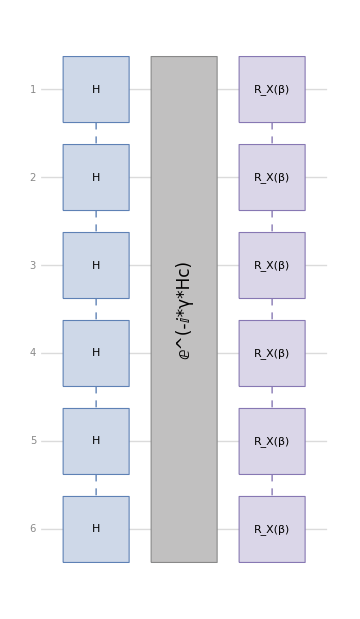

```mathematica
qc["Diagram"]
```

### Mathematica

```mathematica
state=qc[]
```

QuantumState[SparseArray[<64>, {64}], QuantumBasis[<|Input -> QuditBasis[<|{QuditName[I, Dual -> False], 1} -> 1|>], Output -> QuditBasis[<|{QuditName[0, Dual -> False], 1} -> SparseArray[<1>, {2}], {QuditName[1, Dual -> False], 1} -> SparseArray[<1>, {2}], «9», {QuditName[1, Dual -> False], 6} -> SparseArray[<1>, {2}]|>], «2», ParameterSpec -> {{γ, 0, 1}, {β, 0, 1}}|>]]

```mathematica
costFunction="Scalar"//SuperDagger[state]@Hcost@state;
```

```mathematica
cost=Re[ComplexExpand[costFunction]];
```

```mathematica
min=NMinimize[cost,{β,γ}];//AbsoluteTiming
```

{5.45078,Null}

```mathematica
min
```

{7.49601×10^8,{β→0.894448,γ→0.707386}}

```mathematica
result=state[Association@@Last[min]]
```

QuantumState[…]

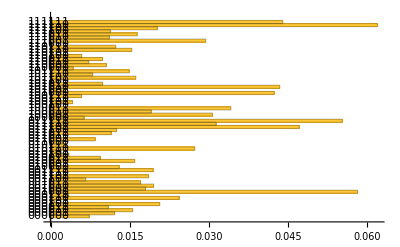

```mathematica
result["ProbabilityPlot",BarOrigin->Left]
```

### Qiskit

```mathematica
circuit=qc[<|β->1.570873617217195,γ->0.5067177460286476|>]["Qiskit"]["Decompose"]["QASM2"]
```

OPENQASM 2.0;
include "qelib1.inc";
gate r(param0,param1) q0 { u(param0,-pi/2 + param1,pi/2 - param1) q0; }
opaque save_statevector q0,q1,q2,q3,q4;
qreg q[5];
u2(-0.25925152772760285,-pi) q[0];
u2(-1.5964834596354145,-pi) q[1];
u2(0.3106322105529058,-pi) q[2];
u3(1.7228677586729602,pi/2,-pi) q[3];
u2(-pi/2,0) q[4];
cx q[4],q[3];
u(1.5727577762710774,1.595237800849806,-1.730946943035668) q[3];
u(pi,1.4480296506245018,3.0188259774193975) q[4];
cx q[4],q[3];
u(1.4187248949168325,-0.6556256605184343,-pi/2) q[3];
u(0,-2.3696985035593103,-1.5995599846757975) q[4];
cx q[4],q[2];
rz(1.333731317082444) q[2];
cx q[3],q[2];
cx q[4],q[2];
rz(0.16751186911018326) q[2];
cx q[3],q[2];
cx q[4],q[1];
rz(0.17238999638482766) q[1];
cx q[3],q[1];
cx q[4],q[1];
rz(-0.3014165131117972) q[1];
cx q[2],q[1];
cx q[4],q[1];
rz(-0.785398163245095) q[1];
cx q[3],q[1];
cx q[4],q[1];
rz(0.0820044354959436) q[1];
cx q[2],q[1];
cx q[4],q[0];
rz(0.06694025014187252) q[0];
cx q[3],q[0];
cx q[4],q[0];
rz(0.46181225248432534) q[0];
cx q[2],q[0];
cx q[4],q[0];
rz(-0.7853981579144711) q[0];
cx q[3],q[0];
cx q[4],q[0];
rz(-0.48876501388033083) q[0];
cx q[1],q[0];
cx q[4],q[0];
rz(-0.78539815160033) q[0];
cx q[3],q[0];
cx q[4],q[0];
rz(0.7853981454044658) q[0];
cx q[2],q[0];
r(1.570873617217195,0) q[2];
cx q[4],q[0];
rz(0.7853981622055362) q[0];
cx q[3],q[0];
r(1.570873617217195,0) q[3];
cx q[4],q[0];
rz(0.21926404241814285) q[0];
cx q[1],q[0];
r(1.570873617217195,0) q[0];
r(1.570873617217195,0) q[1];
r(1.570873617217195,0) q[4];
save_statevector q[0],q[1],q[2],q[3],q[4];

```mathematica
(*chaning u->u3*)
```

from qiskit import qasm2
circuit = qasm2.load('/Users/sebastian/Downloads/test2.txt')

from typing import List, Tuple, Any
import numpy as np

import cirq
from qbraid import QbraidProvider, ConversionGraph, QPROGRAM_REGISTRY, transpile
from qiskit import QuantumRegister, ClassicalRegister, QuantumCircuit
import qiskit
from qbraid_qir.cirq import cirq_to_qir

cirq_circuit = transpile(circuit, "cirq")
qir_circuit = cirq_to_qir(cirq_circuit)

provider = QbraidProvider()
backend = provider.get_device("rigetti.qpu.ankaa-3")
job = backend.run(qir_circuit, shots=1000, entrypoint="main")

provider = QbraidProvider()
backend = provider.get_device("quantinuum.sim.h1-1sc")
job = backend.run(circuit, shots=1000, entrypoint="main")

job.status()

ExternalFunction[…]

## Iterative solution

```mathematica
multiaQAOAclean[Dmatrix_,ω_,{λ3_,λ4_,σ_,c_}]:=Module[{ket,pos,g,gg},
ket=multiQAOAStep[Dmatrix,ω,{λ3,λ4,σ,c}];
Print[ket];
ket=First[ket];
pos=Flatten@Position[First[List@@Keys[ket]],0];
g=WeightedAdjacencyGraph[Dmatrix];
{Normal@WeightedAdjacencyMatrix[VertexDelete[g,pos]],Delete[ω,List/@pos]}
]
```

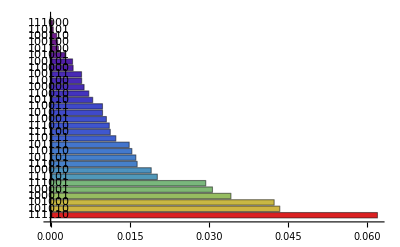

```mathematica
img1=BarChart[Values[#],ChartLabels->Keys[#],BarOrigin->Left,ColorFunction->Function[{height},ColorData["Rainbow"][height]],ImageSize->Full]&@Association[s1]
```

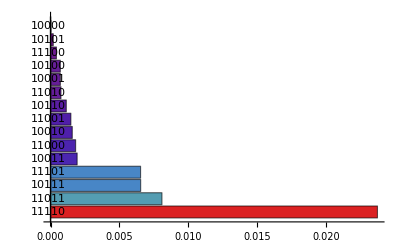

```mathematica
img2=BarChart[Values[#],ChartLabels->Keys[#],BarOrigin->Left,ColorFunction->Function[{height},ColorData["Rainbow"][height]],ImageSize->Full]&@Association[s2]
```

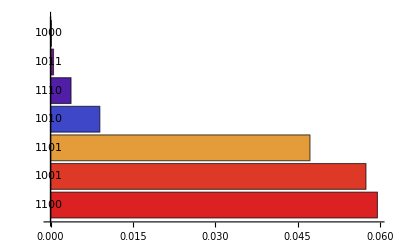

```mathematica
img3=BarChart[Values[#],ChartLabels->Keys[#],BarOrigin->Left,ColorFunction->Function[{height},ColorData["Rainbow"][height]],ImageSize->Full]&@Association[s3]
```